```mathematica
friction[v_]:=-λ*v
```

```mathematica
tmax=10;
v0=5;
λ=0.2;
```

```mathematica
NDSolve[{x'[t]==v[t],v'[t]==friction[v[t]],x[0]==0,v[0]==v0},{x,v},{t,0,tmax}];
xsol=x/.%[[1]]
vsol=v/.%%[[1]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

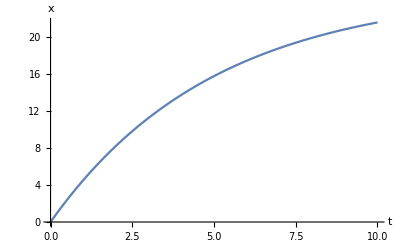

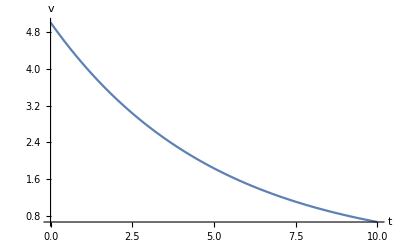

```mathematica
Plot[xsol[t],{t,0,tmax},AxesLabel->{"t","x"}]
Plot[vsol[t],{t,0,tmax},AxesLabel->{"t","v"}]
```

```mathematica
xsol[tmax]
vsol[tmax]
```

21.6166

0.676676

```mathematica
NDSolve[{x'[t]==-v[t],v'[t]==-friction[v[t]],x[0]==xsol[tmax],v[0]==vsol[tmax]},{x,v},{t,0,tmax}];
xsol2=x/.%[[1]]
vsol2=v/.%%[[1]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

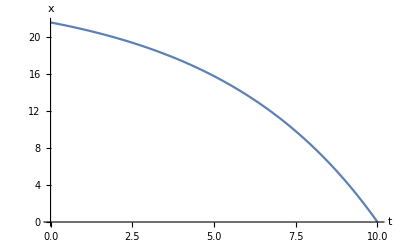

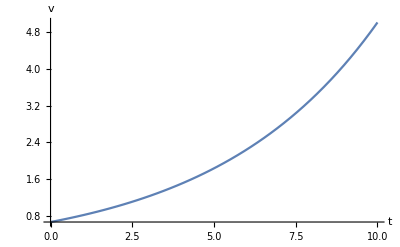

```mathematica
Plot[xsol2[t],{t,0,tmax},AxesLabel->{"t","x"}]
Plot[vsol2[t],{t,0,tmax},AxesLabel->{"t","v"}]
```

```mathematica
xsol2[tmax]
vsol2[tmax]
```

-1.89956×10^-6

5.